```mathematica
(*First we'll clear the Kernel of any unwanted definitions*)
(*Quit[]*)
```

Here, I consider the result of mutant invasion in a cycling population. This occurs when average specialist payoff exceeds average generalist payoff. First I’ll consider the outcome of  an invading alpha mutant along a cycle’s period. Below is our system of equations denoting the frequency of each strategist.

First we’ll create expressions for the frequency of the two specialist host phenotypes, and potential mutants in each phenotype. Each Strategist will have their own associated payoffs:

```mathematica
(*x -> the proportion of a host's resource that is shared*)
(*α -> the matched exchange rate*)
(*(1-α^(1/c))^c -> the mismatched exchange rate, f(α)*)
(*αg -> the generalist exchange rate*)
payoffs={x*(α−x),
x*((1-α^(1/c))^c−x),
x*(αg−x),
x*(1−α),
x*(1−(1-α^(1/c))^c),
x*(1−αg)};(*Payoffs for hosts (1 through 3)and symbionts (4 through 6)*)
```

```mathematica
{pi1,pi1',pig,ψ1,ψ1',ψg1}=payoffs; (*Host 1 payoffs (pi1 - match, pi1' - msimatch and pig - generalist) and payoffs for a symbiont interacting with host 1 (ψ1 - match,ψ1'- mismatch,ψg1 - generalist)*)
{pi1m,pi1m',pig1m,ψ1m,ψ1m',ψg1m}=payoffs/.{α-> αm};
{pi2,pi2',pig2,ψ2,ψ2',ψg2}=payoffs/.{α->α2 };
{pi2m,pi2m',pig2m,ψ2m,ψ2m',ψg2m}=payoffs/.{α->α2m };
(*Payoffs for interactions with and by host 1, the host 1 mutant, host 2 and the host 2 mutant*)
```

Next we find the average payoffs of each strategist:

```mathematica
S1 = v1*ψ1+v2*ψ2'+m1*ψ1m+m2*ψ1m'+(1−v−p-m1-m2)*ψg1; (*Symbiont 1 *)
S2 =  v1*ψ1'+v2*ψ2+m1*ψ1m'+m2*ψ2m+(1−v−p-m1-m2)*ψg1; (*Symbiont 2 *)
H1=u*pi1+(1-u)*pi1';(*Host 1 *)
H2 = u*pi2'+(1−u)*pi2;(*Host 2 *)
HM1=u*pi1m+(1-u)*pi1m';(*Host 1 mutant*)
HM2=u*pi2m+(1-u)*pi2m';(*Host 2 mutant*)
HG = pig;(*Generalist Host*)
Hbar = v1*H1+v2*H2+m1*HM1+m2*HM2+(1-v1-v2-m1-m2)*HG;(*Payoff received by a host on average*)
```

Finally, we’ll find expressions for the frequency of each strategist:

```mathematica
S = u(1-u)(S1-S2);(*Symbiont 1*)
V1=v1(H1-Hbar);(*Host 1*)
V2=v2(H2-Hbar);(*Host 2*)
M1=m1(HM1-Hbar);(*Host 1 Mutant*)
M2=m2(HM2-Hbar); (*Host 2 Mutant*)
```

Now we can put these equations together in a system:

```mathematica
replicators={S,V1,V2,M1,M2}/.{v1-> v1[t],v2-> v2[t],m1-> m1[t],m2-> m2[t], u-> u[t]};
```

```mathematica
{u'[t]==replicators[[1]],v1'[t]==replicators[[2]],v2'[t]==replicators[[3]],m1'[t]==replicators[[4]],m2'[t]==replicators[[5]],u[0]==u0,v1[0]==v10-m10,m1[0]==m10,m2[0]==m20};
```

```mathematica
System[α_,αm_, α2_,α2m_,αg_,c_,x_,u0_,v10_,v20_,m10_,m20_]:={u'[t]==(1-u[t]) u[t] (x (1-αm) m1[t]-x (1-(1-αm^(1/c))^c) m1[t]-x (1-α2m) m2[t]+x (1-(1-αm^(1/c))^c) m2[t]+x (1-α) v1[t]-x (1-(1-α^(1/c))^c) v1[t]-x (1-α2) v2[t]+x (1-(1-α2^(1/c))^c) v2[t]),v1'[t]==v1[t] (x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]-m2[t] (x (-x+(1-α2m^(1/c))^c) (1-u[t])+x (-x+α2m) u[t])-m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t])-(x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-m1[t]-m2[t]-v1[t]-v2[t])-(x (-x+α2) (1-u[t])+x (-x+(1-α2^(1/c))^c) u[t]) v2[t]),v2'[t]==v2[t] (x (-x+α2) (1-u[t])+x (-x+(1-α2^(1/c))^c) u[t]-m2[t] (x (-x+(1-α2m^(1/c))^c) (1-u[t])+x (-x+α2m) u[t])-m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t])-(x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-m1[t]-m2[t]-v1[t]-v2[t])-(x (-x+α2) (1-u[t])+x (-x+(1-α2^(1/c))^c) u[t]) v2[t]),m1'[t]==m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t]-m2[t] (x (-x+(1-α2m^(1/c))^c) (1-u[t])+x (-x+α2m) u[t])-m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t])-(x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-m1[t]-m2[t]-v1[t]-v2[t])-(x (-x+α2) (1-u[t])+x (-x+(1-α2^(1/c))^c) u[t]) v2[t]),m2'[t]==m2[t] (x (-x+(1-α2m^(1/c))^c) (1-u[t])+x (-x+α2m) u[t]-m2[t] (x (-x+(1-α2m^(1/c))^c) (1-u[t])+x (-x+α2m) u[t])-m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t])-(x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-m1[t]-m2[t]-v1[t]-v2[t])-(x (-x+α2) (1-u[t])+x (-x+(1-α2^(1/c))^c) u[t]) v2[t]),u[0]==u0,v1[0]==-m10+v10,v2[0]==v20,m1[0]==m10,m2[0]==m20}(*Here, we format this system appropriately for our simulations note that we begin from initial conditions for u, Subscript[v, 1], v2, v1m and v2m given by u0, v10, v20, v1m0 and v2m0 respectively*)
```

Now we will set up our system with reasonable initial parameters, the tradeoff between matched and mismatching will be concave up.  For now the mutant hosts will be absent. The only hosts present will be host 1 and hosts 2. First we’ll observe the normal cycling of this population:

```mathematica
(*First we test the system to make sure no inappropriate characters remain*)
(*System[α_,αm_, α2_,α2m_,α_,c_,x_,u0_,v10_,v20_,m10_,m20_]*)
System[0.6,0, 0.6,0,0.3,2,0.5,0.6,0.4,0.34,0,0];
```

```mathematica
(*Next we solve this system: *)
sol=NDSolve[System[0.6,0.9, 0.6,0.9,0.3,2,0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
```

```mathematica
(*Store the functions for u(t), Subscript[v, 1](t), Subscript[v, 2](t),Subscript[v, 1] m(t), Subscript[v, 2] m(t)*)
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
```

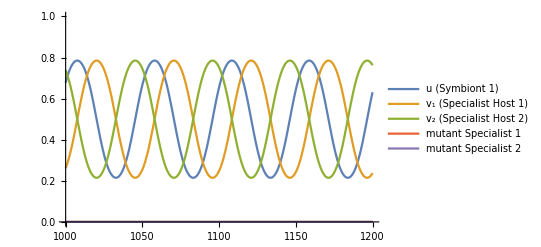

```mathematica
(*Plot*)
Plot[{uans,v1ans,v2ans,m1ans,m2ans},{t,1000,1200}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
(*Reviewing the plot below, note that these initial parameters predispose our system toward having an especially large amplitude, which will make invasion more difficult for mutants that extract more than residents since if they invade at a trough, the population will be largely composed of the symbiont they prefer less. *)
```

Next, we’ll add a mutant host at a point in the cycle:

{0.774366,0.406849,0.593151,0.,0.}

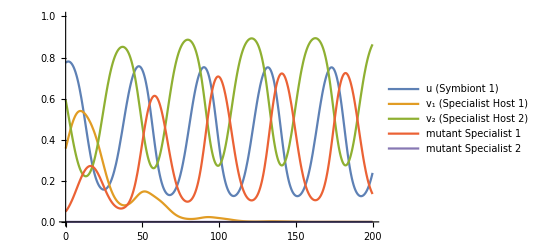

```mathematica
sol=NDSolve[System[0.6,0.9, 0.6,0.9,0.3,2,0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
{uf, v1f,v2f,m1f,m2f}={u[1257],v1[1257],v2[1257],m1[1257],m2[1257]}/.Flatten[sol] (*Find the value of the function when t=1257*)
(*Add a new host 1 mutant at this point in time whose frequency is 0.05: *)
sol=NDSolve[System[0.6,0.9, 0.6,0,0.3,2,0.5,uf,v1f,v2f,0.05,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
Plot[{uans,v1ans,v2ans,m1ans,m2ans},{t,0,200}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
```

We see here that this host introduced at an arbitrary time point successfully invades. Now let’s more systematically consider the outcome of invasion across a cycle’s period. To do so first we need to find the length of a cycle’s period, and define a function to find the average of an NDSolve output.

```mathematica
(*A function to find the average of an interpolating function over a given period in time from a to b:*)
FindAverage[fun_,a_,b_]:=(1/(b-a))*NIntegrate[fun,{t,a,b},WorkingPrecision->4];
(*Next we'll find the cycle's period by comparing the difference in time between two different extrema: *)
sol=NDSolve[System[0.6,0.9, 0.6,0.9,0.3,2,0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
Plot[{uans,v1ans,v2ans,m1ans,m2ans},{t,1000,1200}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
(*Period of v1(t): *)
FindMinimum[{v1ans,1030≤t≤1060},t](*First trough*)
FindMinimum[{v1ans,1070≤t≤1100},t](*Second Trough*)
(*Period of v2(t): *)
FindMinimum[{v2ans,1005≤t≤1050},t]
FindMinimum[{v2ans,1055≤t≤1100},t]
(*Period of u(t) *)
FindMinimum[{uans,1010≤t≤1050},t]
FindMinimum[{uans,1060≤t≤1100},t]
```

-Graphics-

{0.214796,{t→1045.35}}

{0.214796,{t→1095.73}}

{0.214796,{t→1020.17}}

{0.214796,{t→1070.54}}

{0.214797,{t→1032.76}}

{0.214797,{t→1083.13}}

A great sanity check! All of the functions have the same period of 50.4 timesteps. Now let’s consider what happens when we introduce a host 1 mutant with an increased value of alpha along the entirety of this period. First, we’ll see if the frequency of the mutant decreases shortly after the mutant is introduced:

```mathematica
Do[sol=NDSolve[System[0.6,0.9, 0.6,0.9,0.3,2,0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
(*Note that in order to consider the most extreme scenario that would lead to mutant extinction, mutants have a value of alpha that is 0.5 times greater than that of residents. *)
{uf, v1f,v2f,m1f,m2f}={u[st],v1[st],v2[st],m1[st],m2[st]}/.Flatten[sol];
                   sol=NDSolve[System[0.6,0.9, 0.6,0,0.3,2,0.5,uf,v1f,v2f,0.05,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
{min,time}=FindMinimum[{m1ans,10≤t≤100},t];
If[min <0.05,Print["t0 = ", st, ", min = ", min],Unevaluated[Sequence[]]];
,
{st,1255,1306,1}];
```

t0 = 1264, min = 0.0383412

t0 = 1265, min = 0.03533

t0 = 1266, min = 0.0326149

t0 = 1267, min = 0.0302014

t0 = 1268, min = 0.0280862

t0 = 1269, min = 0.0262592

t0 = 1270, min = 0.0247064

t0 = 1271, min = 0.0234122

t0 = 1272, min = 0.0223606

t0 = 1273, min = 0.021537

t0 = 1274, min = 0.0209285

t0 = 1275, min = 0.020525

t0 = 1276, min = 0.0203197

t0 = 1277, min = 0.0203098

t0 = 1278, min = 0.0204967

NDSolve::ndsz: At t == 689.749, step size is effectively zero; singularity or stiff system suspected.

t0 = 1279, min = 0.0208863

t0 = 1280, min = 0.0214888

t0 = 1281, min = 0.0223187

t0 = 1282, min = 0.023394

NDSolve::ndsz: At t == 680.982, step size is effectively zero; singularity or stiff system suspected.

t0 = 1283, min = 0.0247338

NDSolve::ndsz: At t == 391.363, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

t0 = 1284, min = 0.0263568

t0 = 1285, min = 0.0282792

t0 = 1286, min = 0.0308823

t0 = 1287, min = 0.0345957

t0 = 1288, min = 0.039677

t0 = 1289, min = 0.046439

This phenomenon is not uncommon. Let’s see if there are any particular points in the cycle where the mutant goes extinct:

```mathematica
Do[sol=NDSolve[System[0.6,0.9, 0.6,0.9,0.3,2,0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
{uf, v1f,v2f,m1f,m2f}={u[st],v1[st],v2[st],m1[st],m2[st]}/.Flatten[sol];
                   sol=NDSolve[System[0.6,0.9, 0.6,0,0.3,2,0.5,uf,v1f,v2f,0.05,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
avg=FindAverage[m1ans,0,400];(*We consider the average frequency of mutants after they invade. If this number is extremely low the mutant does not successfully invade*)
If[avg <0.05,Print["mutant goes extinct when mutants invade at t = ", st],Unevaluated[Sequence[]]];
,
{st,1255,1315,0.25}];
```

NDSolve::ndsz: At t == 689.707, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 406.746, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 689.749, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

mutant goes extinct when mutants invade at t = 1284.25

So on t whole, even in conditions that predispose mutants toward extinction, this phenomenon is relatively rare. In this case the mutant only successfully invaded at the absolute lowest frequency of their preferred symbiont.

```mathematica
sol=NDSolve[System[0.6,0.9, 0.6,0.9,0.3,2,0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
{uf, v1f,v2f,m1f,m2f}={u[1284.25],v1[1284.25],v2[1284.25],m1[1284.25],m2[1284.25]}/.Flatten[sol]
```

{0.215051,0.514645,0.485355,0.,0.}